```mathematica
teoricos = Import["teorico.csv", "Dataset", "HeaderLines"->1];
```

```mathematica
ejec = Import["C:\\Users\\pdbru\\Desktop\\tesis\\ADC-pauli-quantum.csv", "Dataset", "HeaderLines"->1];
```

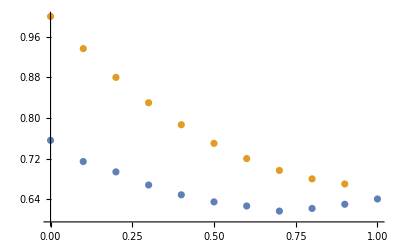

```mathematica
ScoreParaDatasetYP[ds_, p_] = ds[Select[(#chA == "ADC" && #chB == "ADC" && #d =="fidelity" && #pA ==p && #pB ==p)&], "score"][1];
ps = {0, 0.1,0.2,0.3,0.4,0.5,0.6,0.7,0.8, 0.9, 1};
ListPlot[{Table[{p, ScoreParaDatasetYP[ejec, p]}, {p, ps}], Table[{p, ScoreParaDatasetYP[teoricos, p]}, {p, ps}]}]
```

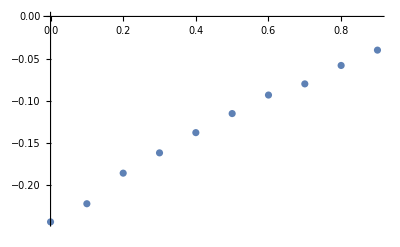

```mathematica
ListPlot[Table[{p, ScoreParaDatasetYP[ejec, p] - ScoreParaDatasetYP[teoricos, p]}, {p, ps}]]
```